```mathematica
d=1;
U01=1;
U02=0;
a=4;
b=1;
n=10;
Rsink=1;
Rmax=10;
t0=0;
t1=10;
datapoints =3;
u1[r_]:=U01 Exp[-((r-a)/b)^n];
u2[r_]:=U02 Exp[-((r-a)/b)^n];
pde = {D[ρ1[r,t],t]==2/r ρ1[r,t] u1'[r]+D[ρ1[r,t],r]u1'[r]+ρ1[r,t] u1''[r]+d 2/r D[ρ1[r,t],r]+d D[ρ1[r,t],r,r]-w12 ρ1[r,t] + w21 ρ2[r,t],
D[ρ2[r,t],t]==2/r ρ2[r,t] u2'[r]+D[ρ2[r,t],r]u2'[r]+ρ2[r,t] u2''[r]+d 2/r D[ρ2[r,t],r]+d D[ρ2[r,t],r,r]-w21 ρ2[r,t] + w12 ρ1[r,t]
};
bc = {
ρ1[Rsink,t]==0,
ρ2[Rsink,t]==0,
ρ1[Rmax,t]==w21/(w12+w21),
ρ2[Rmax,t]==w12/(w12+w21)
};
ic = {
ρ1[r,t0]==w21/(w12+w21)*(1-1/(1+Exp[10 (r-Rmax/2)])),
ρ2[r,t0]==w12/(w12+w21)*(1-1/(1+Exp[10 (r-Rmax/2)]))
};
```

```mathematica
Densities=Table[{0,0,0},{i,1,datapoints}];
ReactionRate=Table[{0,0},{i,1,datapoints}];
```

```mathematica
For[i=1,i<=datapoints,i++,
rd = Exp[-1+i];
w = rd^2*d/2;
w12=w;
w21=w;
sol=NDSolve[{pde,bc,ic},{ρ1,ρ2},{t,t1,t1},{r,Rsink,Rmax},MaxSteps->Infinity,MaxStepFraction->0.002,AccuracyGoal->15,StartingStepSize->0.001,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->1000}}];
Print["Done",i];
ρ1eq[r_]=ρ1[r,t1]/.sol;
ρ2eq[r_]=ρ2[r,t1]/.sol;
ρtot[r_]=(ρ1[r,t1]+ρ2[r,t1])/.sol;
Densities[[i+1,1]]=ρ1eq[r];
Densities[[i+1,2]]=ρ2eq[r];
Densities[[i+1,3]]=ρtot[r];
ReactionRate[[i+1,1]]=rd;
ReactionRate[[i+1,2]]=D[ρtot[r],r]/.r->1;
]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable r.

Done1

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable r.

Done2

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable r.

General::stop: Further output of NDSolve :: mxsst will be suppressed during this calculation.

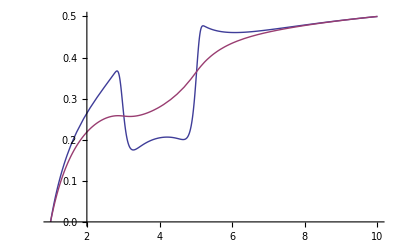

```mathematica
Plot[{ρ1[r,t1]/.sol,ρ2[r,t1]/.sol},{r,1,Rmax}]
Plot[(ρ1[r,t1]+ρ2[r,t1])/.sol,{r,1,Rmax}]
```

```mathematica
ρ1eq[r_]=
+ρ2eq[r,t1])/.sol
```